```mathematica
EllipticTheta[3, I 2 Pi x/s^2, Exp[-4Pi^2/s^2]] == Sum[Exp[-(4 Pi x m + 4 Pi^2 m^2)/s^2], {m, -Infinity, Infinity}, Assumptions->{s > 0}]
```

EllipticTheta[3,(2 ⅈ π x)/s^2,ⅇ^(-(4 π^2)/s^2)]==(ⅇ^(x^2/s^2) Abs[s] EllipticTheta[3,x/2,ⅇ^(-s^2/4)])/(2 √π)

```mathematica
Sum[m Exp[-(4 Pi x m + 4 Pi^2 m^2)], {m, -Infinity, Infinity}]
```

∑_(m=-∞)^∞ ⅇ^(-4 m^2 π^2-4 m π x) m

```mathematica
D[EllipticTheta[3, 2 Pi I x, Exp[-4 Pi^2]], x]
```

2 ⅈ π EllipticThetaPrime[3,2 ⅈ π x,ⅇ^(-4 π^2)]

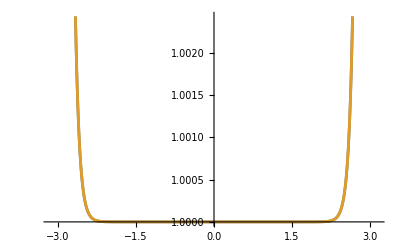

```mathematica
Plot[{EllipticTheta[3,2 ⅈ Pi x,ⅇ^(-4 π^2)], (ⅇ^(x^2) EllipticTheta[3,x/2,1/ⅇ^(1/4)])/(2 √π)}, {x, -Pi, Pi}]
```

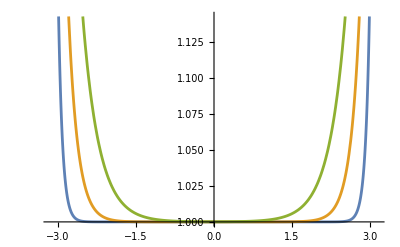

```mathematica
Plot[Evaluate@Table[(ⅇ^(x^2/s^2) Abs[s] EllipticTheta[3,x/2,ⅇ^(-s^2/4)])/(2 √π), {s, 1, 2, 0.5}], {x, -Pi, Pi}]
```

```mathematica
Plot[Evaluate@{
},
{x, -Pi, Pi}]
```

NSum::nsnum: Summand (or its derivative) m Exp[-(4 π x m+4 π^2 m^2)] is not numerical at point m = 15.

$Aborted

```mathematica
v1= Table[NSum[m Exp[-(4 Pi x m + 4 Pi^2 m^2)], {m, -Infinity, Infinity}], {x, -Pi, Pi, 0.1}]
```

{1.,0.28461,0.0810026,0.0230541,0.00656142,0.00186744,0.000531492,0.000151268,0.0000430522,0.0000122531,3.48734×10^-6,9.92531×10^-7,2.82484×10^-7,8.03976×10^-8,2.28819×10^-8,6.51241×10^-9,1.85349×10^-9,5.27522×10^-10,1.50138×10^-10,4.27307×10^-11,1.21616×10^-11,3.4613×10^-12,9.85118×10^-13,2.80374×10^-13,7.97971×10^-14,2.2711×10^-14,6.46376×10^-15,1.83962×10^-15,5.23484×10^-16,1.48673×10^-16,4.12037×10^-17,7.82698×10^-18,-1.14753×10^-17,-5.14124×10^-17,-1.83799×10^-16,-6.46693×10^-16,-2.27247×10^-15,-7.98458×10^-15,-2.80545×10^-14,-9.85719×10^-14,-3.46341×10^-13,-1.2169×10^-12,-4.27568×10^-12,-1.5023×10^-11,-5.27844×10^-11,-1.85463×10^-10,-6.51639×10^-10,-2.28959×10^-9,-8.04467×10^-9,-2.82656×10^-8,-9.93137×10^-8,-3.48947×10^-7,-1.22606×10^-6,-4.30785×10^-6,-0.000015136,-0.0000531817,-0.000186858,-0.000656543,-0.00230682,-0.00810521,-0.0284783,-0.100061,-0.351573}

```mathematica
D[EllipticTheta[3,2 ⅈ π x,ⅇ^(-4 π^2)], x]
```

2 ⅈ π EllipticThetaPrime[3,2 ⅈ π x,ⅇ^(-4 π^2)]

```mathematica
v2 = Table[- ⅈ  EllipticThetaPrime[3,2 ⅈ π x,ⅇ^(-4 π^2)]/2, {x, -Pi, Pi, 0.1}]
```

{1.+0. ⅈ,0.28461+0. ⅈ,0.0810026+0. ⅈ,0.0230541+0. ⅈ,0.00656142+0. ⅈ,0.00186744+0. ⅈ,0.000531492+0. ⅈ,0.000151268+0. ⅈ,0.0000430522+0. ⅈ,0.0000122531+0. ⅈ,3.48734×10^-6+0. ⅈ,9.92531×10^-7+0. ⅈ,2.82484×10^-7+0. ⅈ,8.03976×10^-8+0. ⅈ,2.28819×10^-8+0. ⅈ,6.51241×10^-9+0. ⅈ,1.85349×10^-9+0. ⅈ,5.27522×10^-10+0. ⅈ,1.50138×10^-10+0. ⅈ,4.27307×10^-11+0. ⅈ,1.21616×10^-11+0. ⅈ,3.4613×10^-12+0. ⅈ,9.85118×10^-13+0. ⅈ,2.80374×10^-13+0. ⅈ,7.97971×10^-14+0. ⅈ,2.2711×10^-14+0. ⅈ,6.46376×10^-15+0. ⅈ,1.83962×10^-15+0. ⅈ,5.23484×10^-16+0. ⅈ,1.48673×10^-16+0. ⅈ,4.12037×10^-17+0. ⅈ,7.82698×10^-18+0. ⅈ,-1.14753×10^-17+0. ⅈ,-5.14124×10^-17+0. ⅈ,-1.83799×10^-16+0. ⅈ,-6.46693×10^-16+0. ⅈ,-2.27247×10^-15+0. ⅈ,-7.98458×10^-15+0. ⅈ,-2.80545×10^-14+0. ⅈ,-9.85719×10^-14+0. ⅈ,-3.46341×10^-13+0. ⅈ,-1.2169×10^-12+0. ⅈ,-4.27568×10^-12+0. ⅈ,-1.5023×10^-11+0. ⅈ,-5.27844×10^-11+0. ⅈ,-1.85463×10^-10+0. ⅈ,-6.51639×10^-10+0. ⅈ,-2.28959×10^-9+0. ⅈ,-8.04467×10^-9+0. ⅈ,-2.82656×10^-8+0. ⅈ,-9.93137×10^-8+0. ⅈ,-3.48947×10^-7+0. ⅈ,-1.22606×10^-6+0. ⅈ,-4.30785×10^-6+0. ⅈ,-0.000015136+0. ⅈ,-0.0000531817+0. ⅈ,-0.000186858+0. ⅈ,-0.000656543+0. ⅈ,-0.00230682+0. ⅈ,-0.00810521+0. ⅈ,-0.0284783+0. ⅈ,-0.100061+0. ⅈ,-0.351573+0. ⅈ}

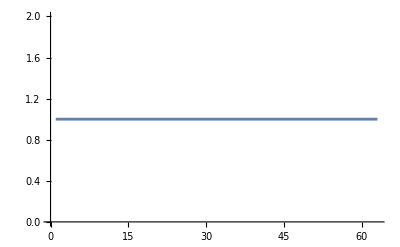

```mathematica
ListPlot[v1/v2, PlotRange->All, Joined->True]
```

```mathematica
Table[- ⅈ  EllipticThetaPrime[3,2 ⅈ π x,ⅇ^(-4 π^2)]/2 / Exp[x^2]EllipticThetaPrime[3, x/2,ⅇ^(-1/4)], {x, -Pi, Pi, 0.1}]
```

{1.74112×10^-22+0. ⅈ,7.87919×10^-8+0. ⅈ,9.35302×10^-8+0. ⅈ,8.75236×10^-8+0. ⅈ,7.48803×10^-8+0. ⅈ,6.06226×10^-8+0. ⅈ,4.68932×10^-8+0. ⅈ,3.47534×10^-8+0. ⅈ,2.46955×10^-8+0. ⅈ,1.68277×10^-8+0. ⅈ,1.09946×10^-8+0. ⅈ,6.8867×10^-9+0. ⅈ,4.13452×10^-9+0. ⅈ,2.37856×10^-9+0. ⅈ,1.31083×10^-9+0. ⅈ,6.91792×10^-10+0. ⅈ,3.49476×10^-10+0. ⅈ,1.6891×10^-10+0. ⅈ,7.80599×10^-11+0. ⅈ,3.44674×10^-11+0. ⅈ,1.45275×10^-11+0. ⅈ,5.83789×10^-12+0. ⅈ,2.2332×10^-12+0. ⅈ,8.11525×10^-13+0. ⅈ,2.79337×10^-13+0. ⅈ,9.07014×10^-14+0. ⅈ,2.76087×10^-14+0. ⅈ,7.79897×10^-15+0. ⅈ,2.00782×10^-15+0. ⅈ,4.53193×10^-16+0. ⅈ,7.94745×10^-17+0. ⅈ,4.60016×10^-18+0. ⅈ,9.43917×10^-18+0. ⅈ,1.09828×10^-16+0. ⅈ,5.89269×10^-16+0. ⅈ,2.54194×10^-15+0. ⅈ,9.70266×10^-15+0. ⅈ,3.38864×10^-14+0. ⅈ,1.1006×10^-13+0. ⅈ,3.35525×10^-13+0. ⅈ,9.65675×10^-13+0. ⅈ,2.6341×10^-12+0. ⅈ,6.82821×10^-12+0. ⅈ,1.68545×10^-11+0. ⅈ,3.96738×10^-11+0. ⅈ,8.916×10^-11+0. ⅈ,1.91471×10^-10+0. ⅈ,3.93205×10^-10+0. ⅈ,7.72629×10^-10+0. ⅈ,1.45335×10^-9+0. ⅈ,2.61811×10^-9+0. ⅈ,4.51832×10^-9+0. ⅈ,7.47237×10^-9+0. ⅈ,1.18452×10^-8+0. ⅈ,1.80017×10^-8+0. ⅈ,2.62326×10^-8+0. ⅈ,3.66569×10^-8+0. ⅈ,4.91109×10^-8+0. ⅈ,6.30233×10^-8+0. ⅈ,7.72034×10^-8+0. ⅈ,8.92127×10^-8+0. ⅈ,9.31403×10^-8+0. ⅈ,7.20078×10^-8+0. ⅈ}

## SU(2) Heat Kernel

```mathematica
(* compute the overall normalization *)
Integrate[x Sin[x] Exp[-x^2/σ^2], {x,-Infinity, Infinity}, Assumptions->{σ > 0}]
```

1/2 ⅇ^(-σ^2/4) √π σ^3

```mathematica
ClearAll[K1]
```

```mathematica
K1[θ_, σ_, mmax_] := (2 Exp[σ^2/4])/(Sqrt[Pi] σ^3)NSum[(θ + 2 Pi m)Sin[θ + 2 Pi m] Exp[-(θ + 2 Pi m)^2/σ^2], {m, -mmax, mmax}];
```

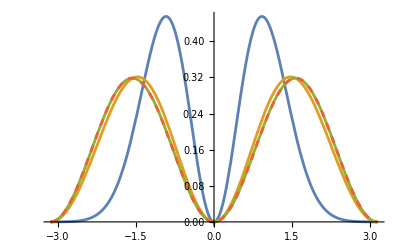

```mathematica
Plot[{K1[x, 1.0, 5], K1[x, 2.0, 10], K1[x, 3.0, 10], K1[x, 4.0, 10]}, {x, -Pi, Pi}, PlotStyle->{{}, { }, {}, Dashed}]
```

```mathematica
K2[θ_, σ_] := (2 Exp[σ^2/4])/(Sqrt[Pi] σ^3)Sin[θ] Exp[-θ^2/σ^2](
θ EllipticTheta[3, 2 Pi θ I / σ^2, Exp[-4 Pi^2/σ^2]] +
-Pi I EllipticThetaPrime[3, 2 Pi θ I / σ^2, Exp[-4 Pi^2/σ^2]]
);
```

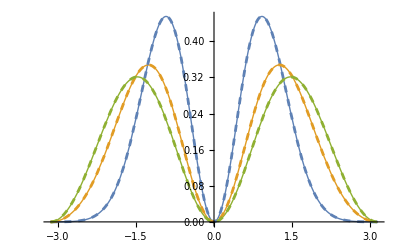

```mathematica
Show[
Plot[{K2[x, 1.0], K2[x, 1.5], K2[x, 2.0]}, {x, -Pi, Pi}, PlotRange->All, PlotStyle->Thin],
Plot[{K1[x, 1.0, 5], K1[x, 1.5, 10], K1[x, 2.0, 10]}, {x, -Pi, Pi}, PlotStyle->Dashed]
]
```

```mathematica
K3[θ_, σ_] := - Exp[σ^2/4]/(4 Pi)Sin[θ] EllipticThetaPrime[3, θ/2, Exp[-σ^2/4]];
K4[θ_, σ_] := Exp[σ^2/4]/(2 Pi)Sin[θ] Sum[m Exp[-σ^2 m^2/4] Sin[m θ], {m, -10, 10}];
```

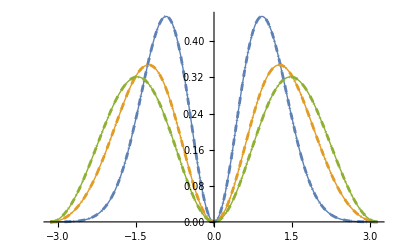

```mathematica
Show[
Plot[{K2[x, 1.0], K2[x, 1.5], K2[x, 2.0]}, {x, -Pi, Pi}, PlotRange->All, PlotStyle->Thin],
Plot[{K3[x, 1.0], K3[x, 1.5], K3[x, 2.0]}, {x, -Pi, Pi}, PlotStyle->Dashed],
Plot[{K4[x, 1.0], K4[x, 1.5], K4[x, 2.0]}, {x, -Pi, Pi}, PlotStyle->Dotted]
]
```

## SU(N) Heat Kernel

The modular transformation of the Jacobi theta functions above comes essentially from Poisson resummation, going to the dual space to the eigenvalues. In general, this should be equivalent to looking at the heat kernel written using the character expansion: K(θ, σ) = ∑_r d_r e^(-σ^2C_r^(2)/2)χ_r(θ). Here the dimension, quadratic Casimir, and value of the character in each representation ‘r’ enters the calculation.

```mathematica
(* NOTES: (1) m = 2j + 1, (2) we multiply by sin^2(θ) for haar measure, (3) normalization obtained by numerology *)
Kp[θ_, σ_] := Exp[σ^2/4]/Pi Sin[θ] Sum[m Exp[-σ^2 m^2/4] Sin[m θ], {m, 1, 10}];
```

We had to a be a little careful about normalization, because C_r^(2) is normalized in different ways, but in the definition above it should correspond to j(j+1) = (m^2-1)/4.

```mathematica
Show[
Plot[{K3[x, 1.0], K3[x, 1.5], K3[x, 2.0]}, {x, -Pi, Pi}, PlotRange->All, PlotStyle->Thin],
Plot[{Kp[x, 1.0], Kp[x, 1.5], Kp[x, 2.0]}, {x, -Pi, Pi}, PlotStyle->Dashed]
]
```

-Graphics-

For SU(3) we have irreps labeled by p, q and corresponding d_r = (p+1)(q+1)(p+q+2)/2, C_r = (p^2+q^2+3p +3q + pq)/3, and χ_r is known but kind of messy. Baaquie has an explicit form in a paper somewhere.